## Matrices

```mathematica
Clear[eq,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
G[χ_, η_]=1+χ η ct ctp;
Λ1byτ=-h1+λ1+a1 ct(* Cos[θ] *);
Λ2byτ=-h2+λ2+a2 ct;

lhs1=λ1+a1 ct;
lhs2=λ2+a2 ct;    
rhs1=1/2 βintra intθpf1(-h1+λ1+a1 ctp)G[1,1];
rhs2=1/2 βintra intθpf2(-h2+λ2+a2 ctp)G[-1,-1];

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn1+eqn2 ct//FullSimplify

eq=lhs2-rhs2;
eqn3=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn3+eqn4 ct//FullSimplify
```

True

True

```mathematica
Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0},{λ1,a1}];
array=(Normal[arr]//FullSimplify)/.ctp->ct;
cmat1=array[[1]]//Expand;cmat2=array[[2]];
rep1={ct h1 intθpf1->hct1,ct h2 intθpf2->hct2,h1 intθpf1->hzero1,h2 intθpf2->hzero2,ct^2 intθpf1->ctct1,ct^2 intθpf2->ctct2,ct intθpf1->ct1,ct intθpf2->ct2,intθpf1->zero1,intθpf2->zero2};
MatrixForm[cmat1/.rep1]//FullSimplify
MatrixForm[cmat2/.rep1]//FullSimplify
```

((hzero1 βintra)/2
(hct1 βintra)/2)

(1-(zero1 βintra)/2 | -(ct1 βintra)/2
-(ct1 βintra)/2 | 1-(ctct1 βintra)/2)

## prel

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,c,v0,ϕ,θp,ϕp,kf,μeff,μ,s} ∈ Reals && k>0 && kf>0 && 0<=θ<=π && 0<=θp<=π && c>0 && v0>0 && μ>0;
repl={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
srep={kf->kf1[θ],(s v0)/(√(kf1[θ]^2))->(s v0)/kf1[θ]};
```

## Fermi surfaces

```mathematica
Solve[k ( c k+s v0)==μeff,k]/.{s^2->1,μeff->μ-s B mbohr}
```

{{k→(-s v0-√(v0^2+4 c (-B mbohr s+μ)))/(2 c)},{k→(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c)}}

## phys qty

```mathematica
Print["zeroth band vel, vvec:"]
vvec = FullSimplify[Grad[ c  (kx^2+ky^2+kz^2)+s v0 √(kx^2+ky^2+kz^2),{kx,ky,kz}],ass];
vvec=FullSimplify[FullSimplify[vvec/.repl,ass]/.srep]
Clear[s,mvec,Bvec,kf,dotprod];
mvec=(-e v0 { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) (* -Graphics-*);
Bvec=B{0,0,1};
Print["BC vector:"](* -Graphics- *);
Ωvec=-s/(2(kf1[θ])^3)FullSimplify[{kx,ky,kz}/.repl,Assumptions->ass]/.srep
Print["omm energy:"];
 dotprod=-mvec.Bvec;
FullSimplify[dotprod/.repl,ass]/.srep
Print["omm velocity:"];
 vomm=om FullSimplify[Grad[dotprod,{kx,ky,kz}]/.repl,ass]/.srep

Print["tot vel. velocity, z-xomp"];
vtot=(vomm+vvec)//FullSimplify;
vtot[[3]]

Print["vtot.k:"];
FullSimplify[kf1[θ]FullSimplify[vtot.{ Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}]//TrigExpand]
Print["Ω.vtot:"];
FullSimplify[Expand[vtot.Ωvec]/.s^2->1]
```

zeroth band vel, vvec:

{Cos[ϕ] (s v0+2 c kf1[θ]) Sin[θ],(s v0+2 c kf1[θ]) Sin[θ] Sin[ϕ],Cos[θ] (s v0+2 c kf1[θ])}

BC vector:

{-(s Cos[ϕ] Sin[θ])/(2 kf1[θ]^2),-(s Sin[θ] Sin[ϕ])/(2 kf1[θ]^2),-(s Cos[θ])/(2 kf1[θ]^2)}

omm energy:

(B e v0 Cos[θ])/(2 kf1[θ])

omm velocity:

{-(B e om v0 Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B e om v0 Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)}

tot vel. velocity, z-xomp

s v0 Cos[θ]-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)+2 c Cos[θ] kf1[θ]

vtot.k:

-(B e om v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2

Ω.vtot:

(B e om s v0 Cos[θ]-2 kf1[θ]^2 (v0+2 c s kf1[θ]))/(4 kf1[θ]^4)

## sigma trials

```mathematica
Clear[sig,s,c,μ,B,v0];
sig[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]:=Block[{e=1,βinter =0,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,cs,λ1,λ2,a1,a2,cost,θp,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},

kf1[θ_]=kF[B,μ,c,v0,s,mbohr,θ,χ];
kf1vec[θ_]=kf1[θ]{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(- χ B e v0)/(2 kf1[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=-(B e χ v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2;
h1[θ_]=1/Dphase1[θ](s v0 Cos[θ]-(B e χ v0 Cos[2 θ])/(2 kf1[θ]^2)+2 c Cos[θ] kf1[θ]+e B χ((B e χ s v0 Cos[θ]-2 kf1[θ]^2 (v0+2 c s kf1[θ]))/(4 kf1[θ]^4)));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero1 βintra)}, {1/2 (hct1 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
cs=λ1 zero1-hzero1+a1 ct1;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
{B,mat,colvec,{zero1, hzero1,ct1}}
];
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;sval=-1;bval=1;
Quiet[sig[bval,mu,cval,v0val,1,bohrrm,omval,1]]//Chop
```

{1,{{0,5.96997×10^-6},{5.96997×10^-6,0.666667}},{-3.3745×10^-7,0.00471699},{2.,-6.74899×10^-7,-0.0000119399}}

```mathematica
Clear[sigt,s,c,μ,B,v0];
sigt[B_,μ_,c_,v0_,βintra_,mbohr_]:=Block[{e=1,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,λ11,a11,λ21,a21,sig11,sig21,sig12,sig22,mat1,mat2,c1,c2,mt,mat,ct,cs1,cs2,sol,mat11,mat12,mat22,mat21,c11,c21,c22,c12},
(* sig[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] gives {B,mat,colvec,{zero1, hzero1,ct1}} *)
sig11=sig[B,μ,c,v0,βintra,mbohr,1,1];
sig12=sig[B,μ,c,v0,βintra,mbohr,1,-1];

sig21=sig[B,μ,c,v0,βintra,mbohr,-1,1];
sig22=sig[B,μ,c,v0,βintra,mbohr,-1,-1];

mat11=sig11[[2]]; mat12=sig12[[2]];mat22=sig22[[2]]; mat21=sig21[[2]];
c11=sig11[[3]]; c21=sig21[[3]];c21=sig21[[3]]; c22=sig22[[3]];

mt=ArrayFlatten[{{mat11,0},{0,mat21}}];
ct=Join[c11,c21];(* cs=λ1 zero1-hzero1+a1 ct1; *)
cs1=λ11 sig11[[4,1]]-sig11[[4,2]]+a11 sig11[[4,3]];
cs2=λ21 sig21[[4,1]]-sig21[[4,2]]+a21 sig21[[4,3]];
mat=mt.{λ11,a11,λ21,a21};

sol=Flatten[Solve[{mat[[1]]+ct[[1]]==0,mat[[3]]+ct[[3]]==0,cs1==0,cs2==0},{λ11,a11,λ21,a21}],1];
Print[MatrixForm[mat],"\t",MatrixForm[ct],"\t",cs1,"\t",cs2,"\t",Chop[cs1+cs2]];
{MatrixRank[mt],sol}
];

mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; bohrrm= 3*10^-7  0;bval=100;vin=1;
Quiet[sigt[bval,mu,cval,v0val,vin,bohrrm]]//Chop
```

(0.0601495 a11+0.00539717 λ11
0.670344 a11+0.0601495 λ11
-0.0601495 a21+0.00539717 λ21
0.670344 a21-0.0601495 λ21)	(-0.00338764
0.00462992
0.00338764
0.00462992)	0.00677528-0.120299 a11+1.98921 λ11	-0.00677528+0.120299 a21+1.98921 λ21	-0.120299 a11+0.120299 a21+1.98921 λ11+1.98921 λ21

{2,{λ11→0,a11→0.0563204,λ21→0,a21→0.0563204}}

```mathematica
Solve[{0.007031581205519263 a11+0.00007415786607711805 λ11==-0.00012481802801792593,0.00024963605603585187-0.014063162411038527 a11+1.9998516842678458 λ11==0},{a11,λ11}]
```

{{a11→-0.0177484,λ11→-0.000249636}}

## sig final: use only one eqn from the rank-1 matrix

```mathematica
Clear[sign,s,c,μ,B,v0];
sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]:=Block[{e=1,βinter =0,cond,matr,bc1,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,vdotk2,cs,λ1,a1,cost,θp,Dphase1,Dphase2,h1,vz1,zero1,ct1,ctct1,hzero1,hct1,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1},

kf1[θ_]=(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c);
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ]+2 c kf1[θ]^2;
h1[θ_]=1/Dphase1[θ]((vvec1[θ])[[3]]+ e B(bc1[θ].vvec1[θ]));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hct1 βintra}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
(* choosing wrong matrix elements above give wrong solns; choice can be fixed by the answer from sig0 below *)
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ],{θ,0,π}];
{B,cond}
];
(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] *)
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
Quiet[sign[1,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop
```

{1,0.0000202499}

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-15,15,10}]
```

{{-15,0.0000202503},{-5,0.0000202502},{5,0.0000202496},{15,0.0000202485}}

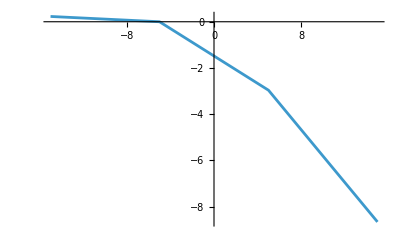

```mathematica
list=dat;
len=Length[list];
x=1/(0.00002025023078744213);
d=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
ListLinePlot[d]
```

## sigma at B=0

```mathematica
Clear[sig0,s,c,μ,B,v0];
sig0[μ_,c_,v0_,βintra_,s_]:=Block[{e=1,B=0,βinter =0,cond,matr,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vdotk1,cs,λ1,λ2,a1,a2,cost,θp,Dphase1,h1,vz1,h2,vz2,zero1,zero2,ct1,ctct1,hzero1,hct1,hct2,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1},

kf1[θ_]=(√(v0^2+4 c μ)-s v0)/(2 c);
Dphase1[θ_]=1;
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vdotk1[θ_]=2 c kf1[θ]^2+s v0 kf1[θ];
h1[θ_]=1/Dphase1[θ](2 c kf1[θ]+s v0 )Cos[θ];
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero1 βintra)}, {1/2 (hct1 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ],{θ,0,π}];
{0,cond}
];
(* sig0[μ_,c_,v0_,βintra_,s_] *)
mu=10.0^-0; cval=5 10^-5 ;v0val= 5 10^-4;sval=-1;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
```

{0,0.00020025}

{0,0.00020025}

## Results

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] *)
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-105,105,10}]
sig0[mu,cval,v0val,1,sval]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {2.32547}. NIntegrate obtained -7.27596×10^-11 and 1.70285×10^-10 for the integral and error estimates.

{0,0.00020025}

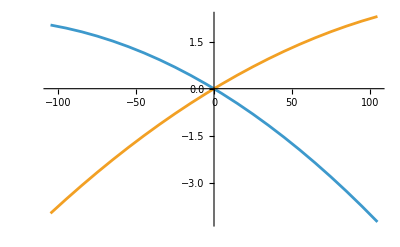

```mathematica
list={{-105,0.00020025407489927306},{-95,0.00020025387853937816},{-85,0.0002002536418173855},{-75,0.00020025336473285477},{-65,0.00020025304728535088},{-55,0.00020025268947444454},{-45,0.00020025229129971216},{-35,0.00020025185276073592},{-25,0.0002002513738571038},{-15,0.00020025085458840925},{-5,0.0002002502949542514},{5,0.00020024969495423505},{15,0.00020024905458797116},{25,0.00020024837385507557},{35,0.00020024765275517058},{45,0.00020024689128788348},{55,0.00020024608945284783},{65,0.0002002452472497027},{75,0.00020024436467809255},{85,0.00020024344173766813},{95,0.0002002424784280853},{105,0.00020024147474900599}};
len=Length[list];
x=1/0.00020024999999999996;
dat11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
list={{-105,0.0002002420228737511},{-95,0.00020024292711792992},{-85,0.00020024380093663766},{-75,0.0002002446443300996},{-65,0.00020024545729854494},{-55,0.00020024623984220586},{-45,0.00020024699196131765},{-35,0.000200247713656119},{-25,0.00020024840492685164},{-15,0.00020024906577376092},{-5,0.0002002496961970951},{5,0.00020025029619710576},{15,0.00020025086577404758},{25,0.00020025140492817883},{35,0.00020025191365976048},{45,0.0002002523919690573},{55,0.00020025283985633673},{65,0.00020025325732187004},{75,0.0002002536443659311},{85,0.0002002540009887975},{95,0.00020025432719074994},{105,0.00020025462297207215}};
x=1/0.00020025;
dat12=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
ListLinePlot[{dat11,dat12}]
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=-1;
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-105,105,10}]
sig0[mu,cval,v0val,1,sval]
```

{{-105,0.0000202312},{-95,0.0000202341},{-85,0.0000202367},{-75,0.0000202391},{-65,0.0000202413},{-55,0.0000202433},{-45,0.000020245},{-35,0.0000202465},{-25,0.0000202478},{-15,0.0000202488},{-5,0.0000202497},{5,0.0000202503},{15,0.0000202506},{25,0.0000202508},{35,0.0000202507},{45,0.0000202504},{55,0.0000202499},{65,0.0000202491},{75,0.0000202481},{85,0.0000202469},{95,0.0000202455},{105,0.0000202438}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {0.0000120929}. NIntegrate obtained 1.55183×10^-11 and 1.65982×10^-10 for the integral and error estimates.

{0,0.00002025}

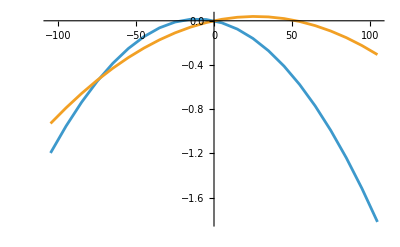

```mathematica
list={{-105,0.00002022579391189924},{-95,0.000020230726175333655},{-85,0.000020235105790415214},{-75,0.00002023893260044856},{-65,0.000020242206459314512},{-55,0.000020244927231467373},{-45,0.00002024709479193309},{-35,0.000020248709026308633},{-25,0.00002024976983076225},{-15,0.000020250277112034773},{-5,0.00002025023078744213},{5,0.000020249630784878644},{15,0.00002024847704282158},{25,0.000020246769510336615},{35,0.00002024450814708426},{45,0.00002024169292332758},{55,0.000020238323819940783},{65,0.000020234400828418728},{75,0.000020229923950887817},{85,0.00002022489320011761},{95,0.000020219308599533627},{105,0.00002021317018323128}};
len=Length[list];
x=1/0.000020249999999999994;
dat21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
list={{-105,0.000020231195438517254},{-95,0.000020234063948542946},{-85,0.000020236705585754592},{-75,0.000020239120350261794},{-65,0.000020241308243958344},{-55,0.00002024326927052086},{-45,0.000020245003435407856},{-35,0.000020246510745858278},{-25,0.000020247791210890806},{-15,0.00002024884484130262},{-5,0.00002024967164966863},{5,0.00002025027165034064},{15,0.000020250644859446516},{25,0.000020250791294889697},{35,0.000020250710976348295},{45,0.000020250403925274797},{55,0.000020249870164895453},{65,0.000020249109720209977},{75,0.00002024812261799106},{85,0.0000202469088867844},{95,0.00002024546855690811},{105,0.00002024380166045305}};
len=Length[list];
x=1/0.000020250000000000004;
dat22=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
ListLinePlot[{dat21,dat22}]
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=-1;
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-105,105,10}]
sig0[mu,cval,v0val,1,sval]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {2.46046}. NIntegrate obtained 1.16529×10^-12 and 2.06674×10^-12 for the integral and error estimates.

{0,0.00020025}

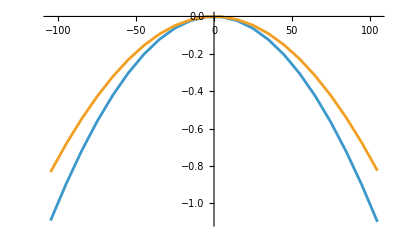

```mathematica
list={{-105,0.00017836469372951982},{-95,0.00018229473812274757},{-85,0.00018584867936681615},{-75,0.00018902082313201082},{-65,0.0001918062087623297},{-55,0.00019420056955149},{-45,0.00019620029961333715},{-35,0.00019780242664856832},{-25,0.00019900459005342338},{-15,0.00019980502393792676},{-5,0.00020020254472613818},{5,0.0002001965431036913},{15,0.0001997869801620844},{25,0.0001989743876680007},{35,0.0001977598724621878},{45,0.00019614512506883457},{55,0.00019413243267564945},{65,0.00019172469672983653},{75,0.0001889254554891562},{85,0.00018573891197376546},{95,0.00018216996788864164},{105,0.00017822426423300377}};
len=Length[list];
x=1/0.00020024999999999996;
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
list={{-105,0.00018357860072979186},{-95,0.0001865725733525728},{-85,0.00018927734258162996},{-75,0.00019168978889973193},{-65,0.00019380718706210555},{-55,0.00019562718954542607},{-45,0.00019714781255311003},{-35,0.00019836742436162594},{-25,0.00019928473583353634},{-15,0.00019989879295852236},{-5,0.00020020897131541482},{5,0.00020021497237701535},{15,0.00019991682160611896},{25,0.0001993148683164061},{35,0.00019840978729642874},{45,0.00019720258221941916},{55,0.00019569459088677435},{65,0.00019388749237946327},{75,0.00019178331622002716},{85,0.00018938445367914873},{95,0.00018669367139570464},{105,0.00018371412751943633}};
len=Length[list];
x=1/0.00020024999999999996;
dat32=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10},{i,1,len}];
ListLinePlot[{dat31,dat32}]
```

## Plots

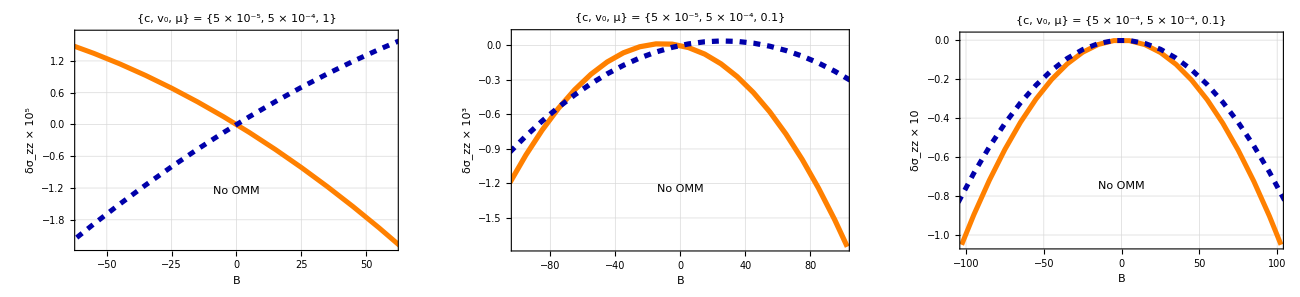

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashed]};

g1=ListPlot[{dat11,dat12},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},{-2.3,1.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^5"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["No OMM",{0,-1.25}],Blue,16,Bold]}];
(*************************)

g2=ListLinePlot[{dat21,dat22},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-1.75,0.1}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^3"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->470,GridLines->Automatic,(*****)Epilog->{Style[Text["No OMM",{0,-1.25}],Blue,16,Bold]}];
(*************************)

g3=ListLinePlot[{dat31,dat32},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-1.05,0.02}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-4,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["No OMM",{0,-0.75}],Blue,16,Bold]}];


leg=LineLegend[style,{"1","-1"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2,g3}},Spacings->{20,0},ImageSize->1300],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["sepnoomm.pdf",Rasterize[pl],ImageResolution->1000];
```